Universidad de Jaén. Escuela Politécnica Superior de Jaén.
Grado en Ingeniería Informática           
Asignatura: Análisis y Métodos Numéricos. Curso 2024/25
F.Javier Muñoz Delgado

# TEMA 13: INTEGRACIÓN NUMÉRICA. Notas y Prácticas

## Integración numérica

## Por qué es necesaria la integración numérica Fórmulas de integración simples: Rectángulo izquierda, rectángulo derecha, punto medio, trapecio, Sipmson. Fórmulas compuestas

## La necesidad

Para calcular integrales definidas, el procedimiento habitual y estudiado en los últimos cursos, consiste en buscar una primitiva de la función y evaluar en los extremos. Sin embargo, puede ocurrirnos que calcular la primitiva sea difícil o imposible, para nosotros o incluso también para el Mathematica. Veamos algunos ejemplos:

```mathematica
∫1/Log[x] ⅆx
```

LogIntegral[x]

```mathematica
∫ⅇ^(x^2)ⅆx
```

1/2 √π Erfi[x]

```mathematica
∫1/(x^5-x^3+1)ⅆx
```

RootSum[1-#1^3+#1^5&,Log[x-#1]/(-3 #1^2+5 #1^4)&]

La primitiva de las funciones 1/Log[x] o de ⅇ^(x^2) precisan de nuevas funciones, no estudiadas por nosotros hasta el momento, por tanto no podríamos encontrar sus primitivas. También las funciones racionales pueden dar problemas pues no tenemos fórmulas para encontrar las raíces de un polinomio cualquiera en el denominador.

También podríamos encontrarnos con funciones experimentales, es decir con funciones de las que no tengamos expresión analítica y solo podamos tener el valor en los puntos que deseemos. Podemos medir la velocidad de un móvil en ciertos instantes (o la temperatura de un objeto,...  ), la teoría nos dice que el espacio recorrido es la integral de la velocidad, pero qué podemos hacer si desconocemos la expresión de la función velocidad?

## Ideas

Al objeto de dar una respuesta a los problemas de integrales definidas, recurrimos a la integración numérica.

En Análisis/Cálculo/Métodos Numéricos siempre hay que tratar de dar respuestas a los problemas. 

Como hacemos con otros problemas, pensamos en qué funciones son fáciles de integrar y aproximamos la función dada por una fácil de integrar.

Una primera respuesta respecto a las funciones fáciles de integrar sería: los polinomios. 

De esta forma, si cuando tengamos que calcular la integral definida de una función f(x) cualquiera, cambiásemos la función dada por un polinomio p(x) que se “pareciese”, podríamos encontrar una aproximación de la integral definida ∫_a^b f(x)ⅆx, si calculamos la integral del polinomio ∫_a^b p(x)ⅆx .

## Fórmulas simples

Una primera idea es interpolar la función con un polinomio de grado bajo (0,1,2, ...) utilizando valores de la función en puntos del intervalo [a,b].

1) Si utilizamos un solo punto, quizás podría ser uno de los extremos o el punto medio.
Rectángulo izquierda ∫_a^b f(x)ⅆx≃∫_a^b f(a)ⅆx = f(a) (b-a) (Se cambia la función por el polinomio constante que interpola en el extremo de la izquierda (a,f(a)) ).
Deducción con el Mathematica: Supongamos que una función en el punto a vale fa. Interpolamos e integramos el polinomio de interpolación en [a,b].

```mathematica
InterpolatingPolynomial[{{a,fa}},x]
```

fa

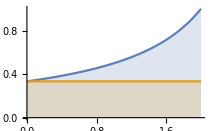

```mathematica
Plot[{1/(3-x),1/3},{x,0,2},AxesOrigin->{0,0},Filling->Axis]
```

```mathematica
∫_a^b faⅆx
```

(-a+b) fa

Rectángulo derecha ∫_a^b f(x)ⅆx≃∫_a^b f(b)ⅆx = f(b) (b-a) (Se cambia la función por el polinomio constante que interpola en el extremo de la derecha (b,f(b)) )
Deducción con el Mathematica: Supongamos que una función en el punto b vale fb. Interpolamos e integramos el polinomio de interpolación en [a,b].

```mathematica
InterpolatingPolynomial[{{b,fb}},x]
```

fb

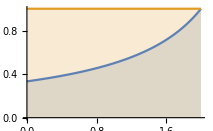

```mathematica
Plot[{1/(3-x),1},{x,0,2},AxesOrigin->{0,0},Filling->Axis]
```

```mathematica
∫_a^b fbⅆx
```

(-a+b) fb

Punto medio ∫_a^b f(x)ⅆx≃∫_a^b f((a+b)/2)ⅆx = f((a+b)/2) (b-a) (Se cambia la función por el polinomio constante que interpola en el punto medio ((a+b)/2,f((a+b)/2)) )
Deducción con el Mathematica: Supongamos que una función en el punto medio del intervalo (a+b)/2 vale fm. Interpolamos e integramos el polinomio de interpolación en [a,b].

```mathematica
InterpolatingPolynomial[{{(a+b)/2,fm}},x]
```

fm

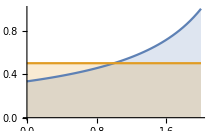

```mathematica
Plot[{1/(3-x),1/2},{x,0,2},PlotRange->All,AxesOrigin->{0,0},Filling->Axis]
```

```mathematica
∫_a^b fmⅆx
```

(-a+b) fm

2) Si utilizamos dos puntos, podrían ser los extremos del intervalo.
Fórmula del Trapecio ∫_a^b f(x)ⅆx≃∫_a^b f(a)+(f(b)-f(a))/(b-a)(x-a)ⅆx = (f(a)+f(b))/2 (b-a) (Se cambia la función por la recta que interpola en los dos extremos  (a,f(a)), (b,f(b)) )
Deducción con el Mathematica: Supongamos que una función en el punto a vale fa y en el punto b vale fb. Interpolamos e integramos el polinomio de interpolación en [a,b].

```mathematica
InterpolatingPolynomial[{{a,fa},{b,fb}},x]
```

fa+((-fa+fb) (-a+x))/(-a+b)

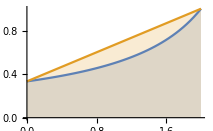

```mathematica
Plot[{1/(3-x),(1+x)/3},{x,0,2},AxesOrigin->{0,0},Filling->Axis]
```

```mathematica
∫_a^b (fa+((-fa+fb) (-a+x))/(-a+b))ⅆx
```

-1/2 (a-b) (fa+fb)

3) Si utilizamos el valor de la función f en tres puntos: extremos, a y b, y su punto medio. 
Fórmula de Simpson: ∫_a^b f(x)ⅆx≃∫_a^b f(a)+(x-a) ((f(b)-f(a))/(b-a)+((2f(b)-4f((a+b)/2)+2f(a)) (x-b))/(b-a)^2)ⅆx = (f(a)+4 f((a+b)/2)+f(b))/6 (b-a) 
(Se cambia la función por la parábola que interpola en los dos extremos y el punto medio (a,f(a)), (b,f(b)), ((a+b)/2,f((a+b)/2)) ).
Deducción con el Mathematica: Supongamos que una función en el punto a vale fa, en el punto b vale fb y en el punto medio, (a+b)/2, vale fm. Interpolamos e integramos el polinomio de interpolación en [a,b].

```mathematica
InterpolatingPolynomial[{{a,fa},{b,fb},{(a+b)/2,fm}},x]//Simplify
```

(b^2 fa+a^2 fb+a b (fa+fb-4 fm)-b (3 fa+fb-4 fm) x-a (fa+3 fb-4 fm) x+2 (fa+fb-2 fm) x^2)/(a-b)^2

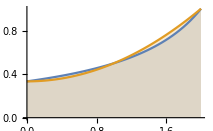

```mathematica
Plot[{1/(3-x),1/6 (2+x^2)},{x,0,2},AxesOrigin->{0,0},Filling->Axis]
```

```mathematica
∫_a^b ((b^2 fa+a^2 fb+a b (fa+fb-4 fm)-b (3 fa+fb-4 fm) x-a (fa+3 fb-4 fm) x+2 (fa+fb-2 fm) x^2)/(a-b)^2)ⅆx
```

-1/6 (a-b) (fa+fb+4 fm)

Observemos que todas las fórmulas tienen elementos comunes. Recordemos que una integral definida es un área, y las fórmulas anteriores tienen un factor común que es la longitud de la base. El otro factor es la altura, que como es variable, se toma un promedio de valores de f(x) (el valor a la izquierda, o a la derecha, o en el punto medio, o la media de los valores en los extremos, o un promedio entre los valores en los extremos y el punto medio). 


					Rectángulo Izquierda | f(a) (b-a)
Rectángulo Derecha | f(b) (b-a)
Punto Medio | f((a+b)/2) (b-a)
Trapecio | (f(a)+f(b))/2(b-a)
Simpson | (f(a)+4 f((a+b)/2)+f(b))/6(b-a)

4) Si utilizamos el valor de la función f en más de tres puntos, podríamos proceder de forma similar: Consideramos puntos equidistantes del intervalo [a,b], interpolamos en esos puntos, e integramos el polinomio de interpolación.
Intervalo: [a,b]
Puntos: 4
Separación entre ellos: h=(b-a)/3
Puntos: a, a+h, a+2h, a +3h. Es decir: 
	a,
	a+h=a+(b-a)/3=(3a+b-a)/3=(2a+b)/3,
	a+2h=a+2(b-a)/3=(3a+2b-2a)/3=(a+2b)/3,
	a+3h=a+3(b-a)/3=(3a+3b-3a)/3=b
Supongamos que en esos puntos f vale f1, f2, f3, f4.

```mathematica
InterpolatingPolynomial[{{a,f1},{(2a+b)/3,f2},{(a+2b)/3,f3},{b,f4}},x]//Simplify
```

1/(2 (a-b)^3)(-2 b^3 f1+2 a^3 f4+b^2 (11 f1-18 f2+9 f3-2 f4) x-9 b (2 f1-5 f2+4 f3-f4) x^2+9 (f1-3 f2+3 f3-f4) x^3+a^2 (b (-2 f1+9 f2-18 f3+5 f4)+(2 f1-9 f2+18 f3-11 f4) x)+a (b^2 (-5 f1+18 f2-9 f3+2 f4)+2 b (7 f1-27 f2+27 f3-7 f4) x-9 (f1-4 f2+5 f3-2 f4) x^2))

```mathematica
∫_a^b (1/(2 (a-b)^3)(-2 b^3 f1+2 a^3 f4+b^2 (11 f1-18 f2+9 f3-2 f4) x-9 b (2 f1-5 f2+4 f3-f4) x^2+9 (f1-3 f2+3 f3-f4) x^3+a^2 (b (-2 f1+9 f2-18 f3+5 f4)+(2 f1-9 f2+18 f3-11 f4) x)+a (b^2 (-5 f1+18 f2-9 f3+2 f4)+2 b (7 f1-27 f2+27 f3-7 f4) x-9 (f1-4 f2+5 f3-2 f4) x^2)))ⅆx//Simplify
```

-1/8 (a-b) (f1+3 f2+3 f3+f4)

La fórmula resultante es: 
∫_a^b f(x)ⅆx≃  (f(a)+3 f((2a+b)/3)+3f((a+2b)/3)+f(b))/8 (b-a) 

De nuevo la longitud del intervalo y una estimación de la altura, haciendo una media ponderada (1 de valor en los extremos y 3 en los dos puntos centrales).

## Fórmulas compuestas

Podríamos continuar deduciendo fórmulas con cada vez más puntos. La coincidencia, cada vez mayor, entre la función y el polinomio de interpolación, nos podría hacer pensar que cada vez tendremos una mejor aproximación, sin embargo, también sabemos que al aumentar el grado del polinomio de interpolación podrían aparecer oscilaciones (recordemos el ejemplo de Runge).

Para mejorar la aproximación, sin utilizar grados elevados, otra idea es dividir el intervalo en subintervalos más pequeños y aplicar una de las fórmulas vistas en cada uno de ellos. Las fórmulas que así aparecen se llamarían fórmulas compuestas, frente a las anteriores que se llamarían fórmulas simples. Veamos algunos ejemplos:

```mathematica
Clear[f,x,a,b,n,xx]
```

```mathematica
f[x_]:=1/Log[x]
```

```mathematica
a=6;
```

```mathematica
b=7;
```

```mathematica
recizq=f[a](b-a);
```

```mathematica
recder=f[b](b-a);
```

```mathematica
punt=f[(a+b)/2](b-a);
```

```mathematica
trap=(f[a]+f[b])/2(b-a);
```

```mathematica
simp=(f[a]+4f[(a+b)/2]+f[b])/6(b-a);
```

```mathematica
{∫_a^b f[x]ⅆx,recizq,recder,punt,trap,simp}//N
```

{0.534829,0.558111,0.513898,0.534244,0.536004,0.534831}

Aquí vemos el valor real y las distintas aproximaciones.

```mathematica
{∫_a^b f[x]ⅆx-recizq,∫_a^b f[x]ⅆx-recder,∫_a^b f[x]ⅆx-punt,∫_a^b f[x]ⅆx-trap,∫_a^b f[x]ⅆx-simp}//N
```

{-0.0232813,0.020931,0.000584885,-0.00117511,-1.77958×10^-6}

Aquí vemos las diferencias entre el valor real y las distintas aproximaciones. Observamos que las fórmulas del rectángulo izquierda y derecha son las menos precisas, que la del punto medio nos da 3 cifras decimales exactas, que la del trapecio nos da dos decimales y que la de Simpson es la que da mejor aproximación pues la diferencia son 2 millonésimas.

Si queremos mejorar estas aproximaciones, podríamos considerar fórmulas compuestas. La idea es dividir el intervalo en varios subintervalos y aplicar en cada uno de ellos una fórmula simple.

Veamos cómo se implementa. Dividiremos el intervalo [a,b] en n subintervalos. En cada uno de ellos aplicaremos alguna de las cinco fórmulas anteriores. Obtenemos así las fórmulas del rectángulo izquierda compuesta, rectángulo derecha compuesta, punto medio compuesta, trapecio compuesta y Simpson compuesta.

```mathematica
n=4;
```

```mathematica
xx=Table[a+i(b-a)/n,{i,0,n}];
```

```mathematica
recizqC=(b-a)1/n∑_(i=1)^n f[xx[[i]]];
```

```mathematica
recderC=(b-a)1/n∑_(i=2)^(n+1) f[xx[[i]]];
```

```mathematica
puntC=(b-a)1/n∑_(i=1)^n f[(xx[[i]]+xx[[i+1]])/2];
```

```mathematica
trapC=(b-a)1/n∑_(i=1)^n (f[xx[[i]]]+f[xx[[i+1]]])/2;
```

```mathematica
simpC=(b-a)1/n∑_(i=1)^n (f[xx[[i]]]+4f[(xx[[i]]+xx[[i+1]])/2]+f[xx[[i+1]]])/6;
```

```mathematica
N[{∫_a^b f[x]ⅆx,recizqC,recderC,puntC,trapC,simpC},20]
```

{0.53482937545850486449,0.54042977418207491638,0.52937670313670077621,0.53479245456887999233,0.53490323865938784629,0.53482938259904927698}

```mathematica
N[{∫_a^b f[x]ⅆx-recizqC,∫_a^b f[x]ⅆx-recderC,∫_a^b f[x]ⅆx-puntC,∫_a^b f[x]ⅆx-trapC,∫_a^b f[x]ⅆx-simpC},20]
```

{-0.005600398723570051887,0.0054526723218040882812,0.00003692088962487215938,-0.000073863200882981802888,-7.1405444124947088588×10^-9}

Podemos ver las distintas aproximaciones obtenidas y el error. Vemos que todas las fórmulas han mejorado al pasar de simples a compuestas. Las del rectángulo izquierda y derecha siguen siendo las menos precisas. La fórmula de Simpson sigue siendo, con diferencia, la más precisa.

## ¿Acelerar la convergencia?

Podemos pensar en una sucesión. El intervalo [a,b] lo podemos dividir en n trozos de igual longitud. Para cada valor de n, tenemos un valor aproximado de la integral. Cuando n tiende a infinito, los valores que obtenemos tienden al valor exacto. No obstante, en algunos casos, nos podría interesar acelerar la  convergencia. Recordando lo que hacíamos en el tema de sucesiones, apliquemos el método Δ^2 de Aitken. Lo haremos sobre la sucesión generada por la fórmula compuesta del punto medio, aunque se podría hacer con cualquier otro método.

```mathematica
Clear[f,x,a,b,n,xx]
```

```mathematica
f[x_]:=1/x
```

```mathematica
a=1;
```

```mathematica
b=2;
```

```mathematica
s[n_]:=(b-a)1/n∑_(i=0)^(n-1) f[a+(i+1/2)(b-a)/n]
```

El valor s(n) es el valor de la aproximación al valor de la integral cuando partimos el intervalo en n trozos y aplicamos la fórmula del punto medio.

```mathematica
{s[1],s[2],s[3],s[4],s[100], Log[2]}//N
```

{0.666667,0.685714,0.689755,0.69122,0.693144,0.693147}

Usando la fórmula vista en el tema de sucesiones, calculamos otra sucesión a partir de la sucesión s(n).

```mathematica
ac[n_]:=s[n+2]-(s[n+2]-s[n+1])^2/(s[n+2]-2s[n+1]+s[n])
```

Incluso podemos calcular la sucesión acelerada “de la acelerada”.

```mathematica
acc[n_]:=ac[n+2]-(ac[n+2]-ac[n+1])^2/(ac[n+2]-2ac[n+1]+ac[n])
```

```mathematica
MatrixForm[Table[{n,N[{s[n],ac[n],acc[n]},10],N[Log[2],10]},{n,1,30}]]
```

(1 | {0.6666666667,0.6908424908,0.6928040753} | 0.6931471806
2 | {0.6857142857,0.6920535403,0.6929439533} | 0.6931471806
3 | {0.6897546898,0.6925169081,0.693014003} | 0.6931471806
4 | {0.6912198912,0.6927391409,0.6930535026} | 0.6931471806
5 | {0.6919078857,0.6928620216,0.6930778218} | 0.6931471806
6 | {0.6922843209,0.6929368696,0.6930938105} | 0.6931471806
7 | {0.6925122411,0.6929857573,0.6931048662} | 0.6931471806
8 | {0.692660554,0.6930194163,0.6931128214} | 0.6931471806
9 | {0.692762413,0.6930435636,0.6931187327} | 0.6931471806
10 | {0.6928353604,0.6930614683,0.6931232433} | 0.6931471806
11 | {0.6928893809,0.6930751082,0.6931267623} | 0.6931471806
12 | {0.6929304951,0.6930857365,0.6931295599} | 0.6931471806
13 | {0.6929625079,0.6930941779,0.6931318204} | 0.6931471806
14 | {0.6929879192,0.6931009933,0.6931336728} | 0.6931471806
15 | {0.6930084264,0.6931065747,0.6931352096} | 0.6931471806
16 | {0.6930252143,0.6931112028,0.6931364986} | 0.6931471806
17 | {0.6930391308,0.693115083,0.6931375902} | 0.6931471806
18 | {0.693050795,0.6931183679,0.6931385228} | 0.6931471806
19 | {0.6930606678,0.6931211734,0.6931393258} | 0.6931471806
20 | {0.6930690982,0.6931235884,0.6931400221} | 0.6931471806
21 | {0.693076354,0.6931256821,0.6931406299} | 0.6931471806
22 | {0.6930826436,0.6931275091,0.6931411634} | 0.6931471806
23 | {0.6930881312,0.6931291127,0.6931416343} | 0.6931471806
24 | {0.6930929477,0.693130528,0.6931420521} | 0.6931471806
25 | {0.693097198,0.6931317834,0.6931424244} | 0.6931471806
26 | {0.6931009677,0.693132902,0.6931427576} | 0.6931471806
27 | {0.6931043265,0.693133903,0.693143057} | 0.6931471806
28 | {0.693107332,0.6931348023,0.693143327} | 0.6931471806
29 | {0.6931100321,0.6931356133,0.6931435714} | 0.6931471806
30 | {0.6931124668,0.6931363471,0.6931437932} | 0.6931471806)

Si observamos el número de cifras decimales exactas en cada método, vemos que se consigue el tercer decimal (0,693) con el método original en el paso 15, con la acelerada en el paso 8 y con la acelerada de la acelerada en el paso 3. De forma similar, el cuarto decimal (0,6931) se consigue en la sucesión inicial en el paso 26, en el 14 en la sucesión acelerada  y en el 7 en la acelerada de la acelerada.

## Integración Romberg

Otro método muy utilizado para acelerar la convergencia en integración numérica es el Método de Romberg. Parte de la regla del trapecio compuesta en el intervalo inicial [a,b].

```mathematica
Clear[f,x,a,b,n,xx]
```

```mathematica
f[x_]:=x^7
```

```mathematica
a=1;
```

```mathematica
b=2;
```

```mathematica
R[0,0]=(b-a)((f[a]+f[b])/2);
```

```mathematica
R[n_,0]:=1/2 R[n-1,0]+(b-a)/2^n∑_(k=1)^(2^(n-1)) f[a+(2k-1)*(b-a)/2^n]
```

```mathematica
R[n_,m_]:=1/(4^m-1)(4^m R[n,m-1]-R[n-1,m-1])
```

```mathematica
Table[Which[j>i,0,True,N[R[i,j],12]],{i,0,6},{j,0,6}]//MatrixForm
```

(64.5 | 0 | 0 | 0 | 0 | 0 | 0
40.79296875 | 32.890625 | 0 | 0 | 0 | 0 | 0
34.1548461914 | 31.9421386719 | 31.87890625 | 0 | 0 | 0 | 0
32.4481515884 | 31.8792533875 | 31.8750610352 | 31.875 | 0 | 0 | 0
32.0184879452 | 31.8752667308 | 31.8750009537 | 31.875 | 31.875 | 0 | 0
31.9108844998 | 31.8750166846 | 31.8750000149 | 31.875 | 31.875 | 31.875 | 0
31.8839719072 | 31.875001043 | 31.8750000002 | 31.875 | 31.875 | 31.875 | 31.875)

En la primera columna de esta matriz los valores que aparecen serían los de la fórmula del trapecio compuesta con 2^(n-1) intervalos (64.5 es el valor del trapecio simple, 40.7929 es el valor que da la fórmula del trapecio con dos intervalos, 34.1548 es el valor que nos da la fórmula del trapecio con cuatro intervalos, ...). En la primera columna aparecen valores exactos si la función f(x) fuese un polinomio de grado uno. 

En la segunda columna aparecen los valores que da la fórmula de Simpson compuesta partiendo el intervalo [a,b] en 2^(n-2) intervalos (32.8906 es el valor del la fórmula de Simpson simple, 31.9421 es el valor que nos da Simpson si partimos el intervalo en 2 trozos, 31.8792 es el valor con Simpson haciendo 4 intervalos, ...) . La fórmula de Simpson da valores exactos si la función f(x) fuese un polinomio de hasta grado tres.

En la tercera columna aparecen valores que serían exactos para funciones f(x) que fuesen hasta de grado 5. En general, la columna m dará valores exactos cuando f(x) sea un polinomio de hasta grado 2m-1.

La convergencia de los valores de la primera columna puede ser muy lenta.
En este ejemplo, f(x)=x^7, el valor exacto de la integral en [1,2] es 31.875. El valor que facilita la fórmula del trapecio, tras dividir el intervalo en 64 trozos es 31.8839, con solo un decimal exacto. La convergencia de los valores de la primera columna parece lento.

Los valores de las otras columnas se construyen combinando los valores de la primera (no tomando más valores de f) y se espera que converjan con mayor rapidez. Los valores que tomaríamos esperando obtener la convergencia más rápida serían los de la diagonal de la matriz.

En este ejemplo, dos decimales exactos, 31.87...,  se consiguen en la diagonal de la matriz en el paso 3, que utiliza los valores de f en 5 puntos (f(1), f(1+1/4), f(1+2/4), f(1+3/4) y f(2)). Con estos puntos, si aplicamos la fórmula del trapecio compuesta obtenemos el valor 34.1548..., pero combinando los valores dados por la fórmula del trapecio hasta ese momento (64.500, 40.7929... y 34.1548...) se consigue el valor 31.8789... que es mucho mejor aproximación del valor exacto, 31.875.